# VYA - Přednášky

## 4. Přednáška

### Úvod - Numerická integrace

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Vrz[x_] := a*x^2 + b*x + c;
Rvnc = {Vrz[x0] == f0, Vrz[x0  + Δx] == fPlus, Vrz[x0 - Δx] == fMinus}
```

{c+b x0+a x0^2==f0,c+b (x0+Δx)+a (x0+Δx)^2==fPlus,c+b (x0-Δx)+a (x0-Δx)^2==fMinus}

```mathematica
Solve[Rvnc, {a, b, c}];
DszABC = Solve[Rvnc, {a, b, c}][[1]];
Integrand = Vrz[x] /. DszABC
Integral = Integrate[Integrand, {x, x0 - Δx, x0 + Δx}] //Simplify
```

-((2 f0-fMinus-fPlus) x^2)/(2 Δx^2)-1/(2 Δx^2)x (-4 f0 x0+2 fMinus x0+2 fPlus x0+fMinus Δx-fPlus Δx)-1/(2 Δx^2)(2 f0 x0^2-fMinus x0^2-fPlus x0^2-fMinus x0 Δx+fPlus x0 Δx-2 f0 Δx^2)

1/3 (4 f0+fMinus+fPlus) Δx

### Simpsonova metoda

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?OddQ
```

```mathematica
{OddQ[3], OddQ[4], EvenQ[4]}
```

{True,False,True}

```mathematica
list = Subscript[a, #] & /@ Range[9]
Trojice = Partition[list, 3, 2]
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9}

{{a_1,a_2,a_3},{a_3,a_4,a_5},{a_5,a_6,a_7},{a_7,a_8,a_9}}

```mathematica
Trojice // Length
```

4

```mathematica
list = Subscript[a, #] & /@ Range[9];
Trojice = Partition[list, 3, 2];

Trojice /. {a_, b_, c_} :> a + 4b + c 
Vydej[{a_, b_, c_}] := a + 4b +c;
Vydej /@ Trojice
{1, 4, 1}.# & /@ Trojice
```

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

```mathematica
?Partition
```

```mathematica
Flatten[Partition[list, 3, 2]]
?Flatten
```

{a_1,a_2,a_3,a_3,a_4,a_5,a_5,a_6,a_7,a_7,a_8,a_9}

```mathematica
?Module
```

```mathematica
Quiet[Remove["Global`*"]];
Simpson[f_, xMin_, xMax_, nBodu_ ?OddQ] := Module[{xka, Δx, yka, trojka, vydej}, 
Δx = (xMax - xMin)/(nBodu - 1);
xka = Range[xMin, xMax, Δx] ;
yka = f /@ xka;
trojka = Partition[yka, 3, 2];
vydej[{a_, b_, c_}] := a + 4b +c;
Δx/3 Total[vydej /@ trojka]
];
Simpson[Sin, 0, Pi, 9]
N[Simpson[Sin, 0, Pi, 9]]
```

1/24 π (2+2 √2+8 Cos[π/8]+8 Sin[π/8])

2.00027

-2/3+4 √6+Log[6]+Sin[5]

9.96413

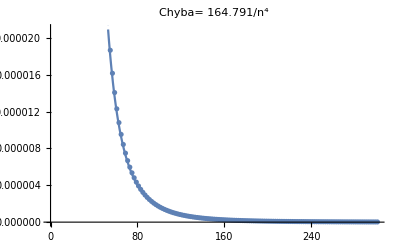

```mathematica
f[x_] := 1/(x+1) + √(x + 1) + Cos[x];
xMin = 0;
xMax = 5;
IntegralPres = Integrate[f[x], {x, xMin, xMax}]
N[IntegralPres]
Chyba[nBodu_ ?OddQ] :=Abs[ (Simpson[f, xMin, xMax, nBodu] - IntegralPres)/IntegralPres] * 100;

{nBMin, nBMax} = {17, 301};
DataChyb = Table[{nBodu, Chyba[nBodu]}, {nBodu, nBMin, nBMax, 2}];
Plt1 = ListPlot[DataChyb];
Proklad = Fit[DataChyb, {1/n^4}, n];
PltProklad = Plot[Proklad, {n, nBMin, nBMax}];
Show[Plt1, PltProklad, PlotLabel -> "Chyba= " <>ToString[TraditionalForm[Proklad]]]
```